```mathematica
(*Some initial definitions.*)
log[z_,branch_:0,branchcut_:-Pi]:=Log[Abs[z]]+I*(Arg[z Exp[-I (branchcut+Pi)]]+branchcut+Pi+2Pi*branch); 
arg[z_,branch_:0,branchcut_:-Pi]:=Arg[z Exp[-I (branchcut+Pi)]]+branchcut+Pi;
F[u_,branch_:0,branchcut_:-Pi]:=(-1/(2Pi*I))log[(u+I)/(u-I),branch,branchcut];
Fsym[u_,branch_:0,branchcut_:-Pi]:=F[u,branch,branchcut]-1/2;
```

```mathematica
(*Creating all possible modenumbers for a given set of string lengths.*)
Mset={2,0,0,0,0};Flatten/@Replace[Tuples[Table[Subsets[Range[-i,i],{Mset[[i]]}],{i,Length[Mset]}]],{}->Nothing,{0,Infinity}]
```

```mathematica
urootsStringHypothesisAcceptingModes[L_,M_,modes_,stringsets_,ϵStart_,ϵSteps_]:=(*MAIN FUNCTION. Produces a list of the uroots, indexed by the mode numbers giving this solution.*)
Module[{Mset,stringsetsPerm,ϵlist,ustart,modesforstring,BAElog,rootfinder,solutions,MM,v,u},

ϵlist=Range[ϵStart,1,(1-ϵStart)/ϵSteps]; (*The list of epislon values to iterate over*)

(*stringsets=Catenate[ Table[Table[i,{j,Mset[[i]]}],{i,Length[Mset]}]];*)(*Alternative, if we supply Mset instead of stringsets*)

BAElog[length_,stringvec_,string_,modenumber_,epsilon_]:=-length*Fsym[2v[string]/stringvec[[string]],-1,0]==-epsilon*Sum[If[string==j,0,If[stringvec[[string]]==stringvec[[j]],0,Fsym[2(v[string]-v[j])/(stringvec[[string]]-stringvec[[j]]),-1,0]]+Fsym[2(v[string]-v[j])/(stringvec[[string]]+stringvec[[j]]),-1,0]+2Sum[If[n==0,0,Fsym[(v[string]-v[j])/n,-1,0]],{n,(stringvec[[string]]-stringvec[[j]])/2+1,(stringvec[[string]]+stringvec[[j]])/2-1}]],{j,1,Length[stringvec]}]+modenumber;

rootfinder[length_,stringvec_,modevec_,startvalues_,epsilon_]:=FindRoot[Table[BAElog[length,stringvec,k,modevec[[k]],epsilon],{k,1,Length[stringvec]}],Table[{v[j],startvalues[[j]]},{j,1,Length[stringvec]}]];

ustart[modevec_,stringvec_]:=Tan[-modevec*Pi/L]*stringvec/2;

solutions=Module[{startvalues,x},startvalues=ustart[modes,stringsets];Nest[Module[{},startvalues=rootfinder[L,stringsets,modes,startvalues,#]//Values//Re;#+(1-ϵStart)/ϵSteps]&,ϵStart,Length[ϵlist]];Table[Chop[startvalues[[s]],10^-10]+I(stringsets[[s]]-1-2k)/2,{s,Length[stringsets]},{k,0,stringsets[[s]]-1}]]//Flatten]
```

```mathematica
urootsStringHypothesis[L_,M_,ϵStart_,ϵSteps_]:= (*MAIN FUNCTION. Produces a list of the uroots, indexed by the mode numbers giving this solution.*)
Module[{Mset,stringsets,stringsetsPerm,ϵlist,modes,ustart,modesforstring,BAElog,rootfinder,solutions,MM,v,u},

ϵlist=Range[ϵStart,1,(1-ϵStart)/ϵSteps]; (*The list of epislon values to iterate over*)

stringsets=Sort/@IntegerPartitions [M]; (*All possible sets of strings; the entry index is labels the string and the entry (some integer) signifies the number of roots in the string.*)

(*
modesforstring[length_,magnon_,stringlength_]:= Range[-stringlength*length/2+stringlength*(magnon-1)/2,stringlength*length/2-stringlength*(magnon-1)/2];

modes=Table[Tuples[modesforstring[L,M,#]&/@stringsets[[i]]],{i,Length[stringsets]}]; (*The list of all possible modes for all possible stringvectors (all entries in stringsets); using modesforstring to iterate ove rall these.*)
modes=Select[DuplicateFreeQ[#]&]/@modes; (*I delete mode numbers that are duplicates*)
modes=Map[DeleteDuplicatesBy[Sort[{Sort[#],Sort[-#]}]&],modes]; (*I delete mode numbers that contain several repeated modes, or are negatives of some other mode number vector.*)
*)
modes={{{0}},{{-1/2,1/2}}};

BAElog[length_,stringvec_,string_,modenumber_,epsilon_]:=-length*Fsym[2v[string]/stringvec[[string]],-1,0]==-epsilon*Sum[If[string==j,0,If[stringvec[[string]]==stringvec[[j]],0,Fsym[2(v[string]-v[j])/(stringvec[[string]]-stringvec[[j]]),-1,0]]+Fsym[2(v[string]-v[j])/(stringvec[[string]]+stringvec[[j]]),-1,0]+2Sum[If[n==0,0,Fsym[(v[string]-v[j])/n,-1,0]],{n,(stringvec[[string]]-stringvec[[j]])/2+1,(stringvec[[string]]+stringvec[[j]])/2-1}]],{j,1,Length[stringvec]}]+modenumber;

rootfinder[length_,stringvec_,modevec_,startvalues_,epsilon_]:=FindRoot[Table[BAElog[length,stringvec,k,modevec[[k]],epsilon],{k,1,Length[stringvec]}],Table[{v[j],startvalues[[j]]},{j,1,Length[stringvec]}]];

ustart[modevec_,stringvec_]:=Tan[-modevec*Pi/L]*stringvec/2;

solutions=Table[{stringsets[[i]],Table[{modes[[i]][[j]],Module[{startvalues,x},startvalues=ustart[modes[[i]][[j]],stringsets[[i]]];Nest[Module[{},startvalues=rootfinder[L,stringsets[[i]],modes[[i]][[j]],startvalues,#]//Values//Re;#+(1-ϵStart)/ϵSteps]&,ϵStart,Length[ϵlist]];Table[Chop[startvalues[[s]],10^-10]+I(stringsets[[i]][[s]]-1-2k)/2,{s,Length[startvalues]},{k,0,stringsets[[i]][[s]]-1}]]},{j,Length[modes[[i]]]}]},{i,Length[stringsets]}];solutions=Replace[solutions,{x_}->x,{0,Infinity}]]
```

```mathematica
urootsStringHypothesisTestforBAENonlogFused[L_,answers_]:=
Module[{BAENonlog,v,x},

BAENonlog[length_,stringvec_,string_]:=Product[((v[string]+I(stringvec[[string]]-1-2k)/2+I/2)/(v[string]+I(stringvec[[string]]-1-2k)/2-I/2))^length,{k,0,stringvec[[string]]-1}]-(*+(-1)^stringvec[[string]] gives the wrong answer!*)(Product[If[string==j,1,Product[Product[(v[string]+I(stringvec[[string]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2+I)/(v[string]+I(stringvec[[string]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2-I),{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[string]]-1}]],{j,1,Length[stringvec]}]);

Table[{answers[[i]][[1]],Select[answers[[i]][[2]],Round[Table[BAENonlog[L,Replace[{answers[[i]][[1]]},{x_List}->x,{0,Infinity}],j],{j,Length[#[[2]]//Re//DeleteDuplicates]}]/.AssociationThread[Table[v[j],{j,1,Length[#[[2]]//Re//DeleteDuplicates]}],#[[2]]//Flatten//Re//DeleteDuplicates],10^-10]==Table[0,{i,Length[(#)[[2]]//Re//DeleteDuplicates]}]&&AllTrue[Abs/@Flatten[#[[2]]],LessThan[10^5]]&]},{i,Length[answers]}](*Provides only those solutions that actually solve the fused BAE (to margin 10^-10) and that are not infinite (norm bigger than 10^5).*)]
```

```mathematica
urootsStringHypothesisTestforBAE[L_,answers_]:=
Module[{BAEfunctions,u,magnon},

magnon=answers[[1]][[1]]//Total;

BAEfunctions=Table[(u[k]+I/2)^L *Product[(u[k]-u[j]-I)^Boole[j!=k],{j,1,magnon}]-(u[k]-I/2)^L*Product[(u[k]-u[j]+I)^Boole[j!=k],{j,1,magnon}],{k,1,magnon}];

Table[{answers[[i]][[1]],Select[answers[[i]][[2]],AllTrue[Abs/@(BAEfunctions/.AssociationThread[Table[u[j],{j,1,magnon}],#[[2]]//Flatten]),LessThan[10]]&&AllTrue[Abs/@Flatten[#[[2]]],LessThan[10^5]]&]},{i,Length[answers]}]
(*Provides only those solutions that actually solve BAE (to margin 10, again excluding norms bigger than 10^5).*)]
```

Some explicit workings. Can be deleted.

```mathematica
answers1=urootsStringHypothesis[4,2,1/10,9]
```

{{2,{0,{ⅈ/2,-ⅈ/2}}},{{1,1},{{-1/2,1/2},{0.288675,-0.288675}}}}

```mathematica
answers2=urootsStringHypothesisTestforBAENonlogFused[7,answers1]
```

{{3,{{-15/2,{0.342365+1. ⅈ,0.342365,0.342365-1. ⅈ}}}},{{1,2},{{{-3/2,-5},{0.221877,{1.33738+0.5 ⅈ,1.33738-0.5 ⅈ}}},{{-3/2,-4},{0.539106,{0.0747215+0.5 ⅈ,0.0747215-0.5 ⅈ}}},{{-3/2,4},{0.683702,{-0.534113+0.5 ⅈ,-0.534113-0.5 ⅈ}}},{{-3/2,5},{0.801478,{-1.60296+0.5 ⅈ,-1.60296-0.5 ⅈ}}},{{-1/2,-5},{-0.0317295,{1.43132+0.5 ⅈ,1.43132-0.5 ⅈ}}},{{-1/2,-4},{0.0652594,{0.330295+0.5 ⅈ,0.330295-0.5 ⅈ}}},{{-1/2,4},{0.220791,{-0.441582+0.5 ⅈ,-0.441582-0.5 ⅈ}}},{{-1/2,5},{0.29652,{-1.50421+0.5 ⅈ,-1.50421-0.5 ⅈ}}}}},{{1,1,1},{{{-3/2,-1/2,1/2},{0.536633,0.10469,-0.18474}},{{-3/2,-1/2,3/2},{0.578739,0.130865,-0.61711}}}}}

```mathematica
answers3=urootsStringHypothesisTestforBAE[7,answers2]
```

{{3,{{-15/2,{0.342365+1. ⅈ,0.342365,0.342365-1. ⅈ}}}},{{1,2},{{{-3/2,-4},{0.539106,{0.0747215+0.5 ⅈ,0.0747215-0.5 ⅈ}}},{{-3/2,4},{0.683702,{-0.534113+0.5 ⅈ,-0.534113-0.5 ⅈ}}},{{-1/2,-4},{0.0652594,{0.330295+0.5 ⅈ,0.330295-0.5 ⅈ}}},{{-1/2,4},{0.220791,{-0.441582+0.5 ⅈ,-0.441582-0.5 ⅈ}}}}},{{1,1,1},{{{-3/2,-1/2,1/2},{0.536633,0.10469,-0.18474}},{{-3/2,-1/2,3/2},{0.578739,0.130865,-0.61711}}}}}

answers42

{{-1,{ⅈ/2,-ⅈ/2}},{{-1/2,1/2},{0.288675,-0.288675}}}

answers73

ustart={{{0.35730060791377566`}},{{-0.5391065371468028`,-0.07472092630508158`},{-0.06593538143525597`,-0.32652958809153904`},{0.2199035743065771`,-0.43270039933726134`},{0.6819739628087789`,-0.5201362025251913`}},{{0.6171097449447068`,-0.13086502350686016`,-0.5787394550456081`},{0.18473976263303082`,-0.10469026132864061`,-0.5366327275602707`}}};

{{15/2,{-0.342365+1. ⅈ,-0.342365,-0.342365-1. ⅈ}},{{3/2,4},{-0.539106,{-0.0747215+0.5 ⅈ,-0.0747215-0.5 ⅈ}}},{{1/2,4},{-0.0652594,{-0.330295+0.5 ⅈ,-0.330295-0.5 ⅈ}}},{{-1/2,4},{0.220791,{-0.441582+0.5 ⅈ,-0.441582-0.5 ⅈ}}},{{-3/2,4},{0.683702,{-0.534113+0.5 ⅈ,-0.534113-0.5 ⅈ}}},{{-3/2,1/2,3/2},{0.61711,-0.130865,-0.578739}},{{-1/2,1/2,3/2},{0.18474,-0.10469,-0.536633}}}

#### Testing code using non-logarithmic BAE:

```mathematica
urootsStringHypothesisNonlog[L_,M_,ϵStart_,ϵSteps_]:= (*MAIN FUNCTION. Produces a list of the uroots, indexed by the mode numbers giving this solution.*)
Module[{Mset,stringsets,stringsetsPerm,ϵlist,modes,ustart,modesforstring,BAElog,solutions,MM,v,u},

ϵlist=Range[ϵStart,1,(1-ϵStart)/ϵSteps]; (*The list of epislon values to iterate over*)

stringsets=Sort/@IntegerPartitions[M]; (*All possible stringvectors; the entries are the strings, with values corresponding to the length of these strings; stringsets[[i]]=="length of string i"*)

BAENonlog[length_,stringvec_,string_,epsilon_]:=Product[(v[string]+I(stringvec[[string]]-1-2k)/2+I/2)^length,{k,0,stringvec[[string]]-1}](Product[If[string==j,1,Product[Product[(v[string]+I(stringvec[[string]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2)-I,{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[string]]-1}]],{j,1,Length[stringvec]}])^epsilon==-(-1)^stringvec[[string]] Product[(v[string]+I(stringvec[[string]]-1-2k)/2-I/2)^length,{k,0,stringvec[[string]]-1}](Product[If[string==j,1,Product[Product[(v[string]+I(stringvec[[string]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2)+I,{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[string]]-1}]],{j,1,Length[stringvec]}])^epsilon;

rootfinderNonlog[length_,stringvec_,startvalues_,epsilon_]:=FindRoot[Table[BAENonlog[length,stringvec,k,epsilon],{k,1,Length[stringvec]}],Table[{v[j],startvalues[[j]]},{j,1,Length[stringvec]}]];

ustartNonlogGenerator[length_,magnon_,stringlength_]:=NSolve[Product[(u+I(stringlength-1-2k)/2+I/2)^length,{k,0,stringlength-1}]==-(-1)^stringlength Product[(u+I(stringlength-1-2kk)/2-I/2)^length,{kk,0,stringlength-1}],u]//Values;

(*ustartNonlogGenerator[length_,magnon_,stringvec_]:=Table[NSolve[Product[(v[string]+I(stringvec[[string]]-1-2k)/2+I/2)^length,{k,0,stringvec[[string]]-1}](Product[If[string==j,1,Product[Product[(v[string]+I(stringvec[[string]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2),{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[string]]-1}]],{j,1,Length[stringvec]}])==-(-1)^stringvec[[string]] Product[(v[string]+I(stringvec[[string]]-1-2k)/2-I/2)^length,{k,0,stringvec[[string]]-1}](Product[If[string==j,1,Product[Product[(v[string]+I(stringvec[[string]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2),{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[string]]-1}]],{j,1,Length[stringvec]}]),u]//Values,{string,Length[stringvec]}];*)

ustartNonlog=Replace[DeleteDuplicates/@Table[Tuples[ustartNonlogGenerator[L,M,#]&/@stringsets[[i]]],{i,Length[stringsets]}],{x_List}->x,{0,Infinity}];

(*ustartNonlog=Replace[DeleteDuplicates/@Tuples[ustartNonlogGenerator[L,M,#]&/@stringsets],{x_List}->x,{0,Infinity}];*)

solutionsNonlog=Table[Module[{startvalues},startvalues=ustartNonlog[[i]][[j]];Nest[Module[{},startvalues=rootfinderNonlog[L,stringsets[[i]],startvalues,#]//Values//Re;#+(1-ϵStart)/ϵSteps]&,ϵStart,Length[ϵlist]];Table[Chop[startvalues[[s]],10^-5]+I(stringsets[[i]][[s]]-1-2k)/2,{s,Length[startvalues]},{k,0,stringsets[[i]][[s]]-1}]],{i,Length[stringsets]},{j,Length[ustartNonlog[[i]]]}];solutionsNonlog=Flatten[solutionsNonlog,1];solutionsNonlog=Replace[solutionsNonlog,{x_}->x,{0,Infinity}];ustartNonlog]
```

```mathematica
urootsStringHypothesisNonlog[4,2,1/10,9]//Quiet
```

#### Everything below can be deleted.

{{15/2,{-0.342365+1. ⅈ,-0.342365,-0.342365-1. ⅈ}},{{3/2,4},{-0.539106,{-0.0747215+0.5 ⅈ,-0.0747215-0.5 ⅈ}}},{{1/2,4},{-0.0652594,{-0.330295+0.5 ⅈ,-0.330295-0.5 ⅈ}}},{{-1/2,4},{0.220791,{-0.441582+0.5 ⅈ,-0.441582-0.5 ⅈ}}},{{-3/2,4},{0.683702,{-0.534113+0.5 ⅈ,-0.534113-0.5 ⅈ}}},{{-3/2,1/2,3/2},{0.61711,-0.130865,-0.578739}},{{-1/2,1/2,3/2},{0.18474,-0.10469,-0.536633}}}

```mathematica
answers42=urootsStringHypothesis[4,2,1/100,99]//Quiet
```

{{-1,{ⅈ/2,-ⅈ/2}},{{-1/2,1/2},{0.288675,-0.288675}}}

```mathematica
answers73=urootsStringHypothesis[7,3,1/100,99]//Quiet
```

{{15/2,{-0.342365+1. ⅈ,-0.342365,-0.342365-1. ⅈ}},{{3/2,4},{-0.539106,{-0.0747215+0.5 ⅈ,-0.0747215-0.5 ⅈ}}},{{1/2,4},{-0.0652594,{-0.330295+0.5 ⅈ,-0.330295-0.5 ⅈ}}},{{-1/2,4},{0.220791,{-0.441582+0.5 ⅈ,-0.441582-0.5 ⅈ}}},{{-3/2,4},{0.683702,{-0.534113+0.5 ⅈ,-0.534113-0.5 ⅈ}}},{{-3/2,1/2,3/2},{0.61711,-0.130865,-0.578739}},{{-1/2,1/2,3/2},{0.18474,-0.10469,-0.536633}}}

```mathematica
answersassoc=AssociationThread[(answers//Transpose)[[1]],(answers//Transpose)[[2]]];
```

```mathematica
length=4;
magnon=2;

BAEfunctions=Table[((Subscript[u, k]+I/2)/(Subscript[u, k]-I/2))^length-Product[((Subscript[u, k]-Subscript[u, j]+I)/(Subscript[u, k]-Subscript[u, j]-I))^Boole[j!=k],{j,1,magnon}],{k,1,magnon}];

correctAnswers=Select[answers,(Round[BAEfunctions/.AssociationThread[Table[Subscript[u, j],{j,1,magnon}],Flatten[(#)[[2]]]],10^-10]/.Indeterminate->0)==Table[0,{i,magnon}]&]//Quiet(*Provides only those solutions that actually solve BAE.*)
```

{{-2,{ⅈ/2,-ⅈ/2}},{-1,{ⅈ/2,-ⅈ/2}},{0,{ⅈ/2,-ⅈ/2}},{1,{ⅈ/2,-ⅈ/2}},{2,{ⅈ/2,-ⅈ/2}},{{-3/2,-3/2},{1.20711,1.20711}},{{-1/2,-1/2},{0.207107,0.207107}},{{-1/2,1/2},{0.288675,-0.288675}},{{1/2,-1/2},{-0.288675,0.288675}},{{1/2,1/2},{-0.207107,-0.207107}},{{3/2,3/2},{-1.20711,-1.20711}}}

```mathematica
nonrepeatedCorrectAnswers=Select[correctAnswers,DuplicateFreeQ[#[[1]]]&]
```

{{{-3/2,1/2,3/2},{0.61711,-0.130865,-0.578739}},{{-1/2,1/2,3/2},{0.18474,-0.10469,-0.536633}}}

```mathematica
BAElog[length_,stringvec_,string_]:=length*Sum[Fsym[2v[string]+I(stringvec[[string]]-1-2k),-1,0],{k,0,stringvec[[string]]-1}]-Sum[If[string==j,0,Sum[Sum[Fsym[v[string]+I(stringvec[[string]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2,-1,0],{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[string]]-1}]],{j,1,Length[stringvec]}];

testsolution[length_,stringvec_,testvalues_]:=Table[BAElog[length,stringvec,k],{k,1,Length[stringvec]}]/.Table[v[j]->testvalues[[j]],{j,1,Length[stringvec]}];
```

```mathematica
answersassoc[{-3/2,-4}]
```

{0.539106,{0.0747215+0.5 ⅈ,0.0747215-0.5 ⅈ}}

```mathematica
startfunction[length_,string_,stringvec_]:=length*Sum[Fsym[2v[string]+I(stringvec[[string]]-1-2k),-1,0],{k,0,stringvec[[string]]-1}]
```

```mathematica
startfunction[length,1,string]/.v[1]->0.0001//N
```

2.00013+0. ⅈ

```mathematica
modes73={{{15/2}},{{3/2,4},{1/2,4},{-1/2,4},{-3/2,4}},{{-3/2,1/2,3/2},{-1/2,1/2,3/2}}}
```

```mathematica
testvalues2={Subscript[u, 1]->0.41421356237309503+0.5 ⅈ,Subscript[u, 2]->0.41421356237309503-0.5 ⅈ};
BAEfunctions
BAEfunctions/.testvalues2
```

{(ⅈ/2+u_1)^4/(-ⅈ/2+u_1)^4-(ⅈ+u_1-u_2)/(-ⅈ+u_1-u_2),(ⅈ/2+u_2)^4/(-ⅈ/2+u_2)^4-(ⅈ-u_1+u_2)/(-ⅈ-u_1+u_2)}

General::munfl: (0.414214+1. ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::munfl: 1/(0.414214-1. ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

{ComplexInfinity,0.-0.0214466 ⅈ}

```mathematica
NSolve[{(ⅈ/2+Subscript[u, 1])^7/(-ⅈ/2+Subscript[u, 1])^7==((ⅈ+Subscript[u, 1]-Subscript[u, 2]) (ⅈ+Subscript[u, 1]-Subscript[u, 3]))/((-ⅈ+Subscript[u, 1]-Subscript[u, 2]) (-ⅈ+Subscript[u, 1]-Subscript[u, 3])),(ⅈ/2+Subscript[u, 2])^7/(-ⅈ/2+Subscript[u, 2])^7==((ⅈ-Subscript[u, 1]+Subscript[u, 2]) (ⅈ+Subscript[u, 2]-Subscript[u, 3]))/((-ⅈ-Subscript[u, 1]+Subscript[u, 2]) (-ⅈ+Subscript[u, 2]-Subscript[u, 3])),(ⅈ/2+Subscript[u, 3])^7/(-ⅈ/2+Subscript[u, 3])^7==((ⅈ-Subscript[u, 1]+Subscript[u, 3]) (ⅈ-Subscript[u, 2]+Subscript[u, 3]))/((-ⅈ-Subscript[u, 1]+Subscript[u, 3]) (-ⅈ-Subscript[u, 2]+Subscript[u, 3]))},{Subscript[u, 1],Subscript[u, 2],Subscript[u, 3]}]
```

{{u_2→-0.0747209-0.5 ⅈ,u_1→-0.539107,u_3→-0.0747209+0.5 ⅈ},{u_2→30557.2-110824. ⅈ,u_1→-2.19062+0.0000248559 ⅈ,u_3→-2.19062+0.0000440664 ⅈ},{u_2→0.0659354,u_1→0.32653-0.500748 ⅈ,u_3→0.32653+0.500748 ⅈ},{u_2→-0.0659354,u_1→-0.32653-0.500748 ⅈ,u_3→-0.32653+0.500748 ⅈ},{u_2→0.219904,u_1→-0.4327-0.503066 ⅈ,u_3→-0.4327+0.503066 ⅈ},{u_2→-0.219904,u_1→0.4327-0.503066 ⅈ,u_3→0.4327+0.503066 ⅈ},{u_2→0.360689-0.991199 ⅈ,u_1→0.357301,u_3→0.360689+0.991199 ⅈ},{u_2→-0.360689-0.991199 ⅈ,u_1→-0.357301,u_3→-0.360689+0.991199 ⅈ},{u_2→-0.681974,u_1→0.520136-0.506422 ⅈ,u_3→0.520136+0.506422 ⅈ},{u_2→0.681974,u_1→-0.520136-0.506422 ⅈ,u_3→-0.520136+0.506422 ⅈ},{u_2→0.1332+0.178242 ⅈ,u_1→0.119796-0.812305 ⅈ,u_3→0.1332+0.178242 ⅈ},{u_2→0.1332+0.178242 ⅈ,u_1→0.119796-0.812305 ⅈ,u_3→0.1332+0.178242 ⅈ},{u_2→0.+0.160655 ⅈ,u_1→0.-0.858391 ⅈ,u_3→0.+0.160655 ⅈ},{u_2→0.-0.160655 ⅈ,u_1→0.-0.160655 ⅈ,u_3→0.+0.858391 ⅈ},{u_2→-0.309807-0.189446 ⅈ,u_1→-0.309807-0.189446 ⅈ,u_3→-0.345712+0.785471 ⅈ},{u_2→-0.309807+0.189446 ⅈ,u_1→-0.345712-0.785471 ⅈ,u_3→-0.309807+0.189446 ⅈ},{u_2→-2.69568,u_1→-6.08367,u_3→-2.69568},{u_2→2.69568,u_1→6.08367,u_3→2.69568},{u_2→0.487957+0.244057 ⅈ,u_1→0.431296-0.799367 ⅈ,u_3→0.487957+0.244057 ⅈ},{u_2→-1.75477,u_1→-1.75477,u_3→0.806149},{u_2→1.75477,u_1→1.75477,u_3→-0.806149},{u_2→-1.66535,u_1→-1.66535,u_3→0.298798},{u_2→1.66535,u_1→1.66535,u_3→-0.298798},{u_2→0.298798,u_1→-1.66535,u_3→-1.66535},{u_2→-1.51576-0.581831 ⅈ,u_1→-1.51576-0.581831 ⅈ,u_3→-1.03738+0.70809 ⅈ},{u_2→-1.51576+0.581831 ⅈ,u_1→-1.51576+0.581831 ⅈ,u_3→-1.03738-0.70809 ⅈ},{u_2→-1.03738-0.70809 ⅈ,u_1→-1.51576+0.581831 ⅈ,u_3→-1.51576+0.581831 ⅈ},{u_2→-1.03738+0.70809 ⅈ,u_1→-1.51576-0.581831 ⅈ,u_3→-1.51576-0.581831 ⅈ},{u_2→-1.51576+0.581831 ⅈ,u_1→-1.03738-0.70809 ⅈ,u_3→-1.51576+0.581831 ⅈ},{u_2→1.51576-0.581831 ⅈ,u_1→1.51576-0.581831 ⅈ,u_3→1.03738+0.70809 ⅈ},{u_2→1.51576+0.581831 ⅈ,u_1→1.03738-0.70809 ⅈ,u_3→1.51576+0.581831 ⅈ},{u_2→1.03738+0.70809 ⅈ,u_1→1.51576-0.581831 ⅈ,u_3→1.51576-0.581831 ⅈ},{u_2→-1.60015,u_1→-1.60015,u_3→0.0337928},{u_2→0.0337928,u_1→-1.60015,u_3→-1.60015},{u_2→-0.218327,u_1→-1.51871,u_3→-1.51871},{u_2→-1.51871,u_1→-1.51871,u_3→-0.218327},{u_2→-1.19897,u_1→-1.19897,u_3→-0.804274},{u_2→1.03826,u_1→1.03826,u_3→1.03826},{u_2→-1.03826,u_1→-1.03826,u_3→-1.03826}}

#### Trying other ways to handle epsilon

```mathematica
Re[1/(x+I/2(s-1-2k-ss+1+2kk))]
```

Re[1/(1/2 ⅈ (-2 k+2 kk+s-ss)+x)]

```mathematica
(*ustart[length_,magnon_,modes_]:=(1/2)Tan[-Pi*(modes)/length]+10^-5/.{ComplexInfinity->10^15};*)(*Older version of ustart; not to be used.*)
ustart[length_,magnon_,stringvec_,modevec_]:=NSolve[Table[-(length/Pi)*Sum[ArcTan[2v[i]+I(stringvec[[i]]-1-2k)],{k,0,stringvec[[i]]-1}]==+I*Pi *Sum[If[i==j,0,Sum[Sum[1+Sign[Re[1/(v[i]+I(stringvec[[i]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2)]],{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[string]]-1}]],{j,1,Length[stringvec]}]+modevec[[i]],{i,Length[stringvec]}],Table[v[i],{i,Length[stringvec]}]];(*Find startvalues by numerically solving the BAElog for epsilon==0; if no solution is found we put 0 as the solution, for lack of better options*)

ustart[4,2,{2},{3}]
```

{{v[1]→-1.}}

```mathematica
length=4;
string={2};
testvalues={0};

Limit[testsolution[length,string,{x}],x->0,Direction->-1]//N
```

{2.}

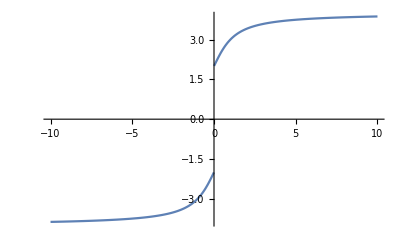

```mathematica
Plot[testsolution[length,string,{x}],{x,-10,10}]
```

```mathematica
ustart[length_,magnon_,stringvec_,modevec_]:=Table[NSolve[-(length/Pi)*Sum[ArcTan[2u[i]+I(stringvec[[i]]-1-2k)],{k,0,stringvec[[i]]-1}]==modevec[[i]],u[i]],{i,Length[stringvec]}];

ustart[4,2,{2},{3}]
```

```mathematica
ustart[length_,magnon_,stringvec_,modevec_]:=Table[NSolve[-length*Sum[Fsym[2u[i]+I(stringvec[[i]]-1-2k),-1,0],{k,0,stringvec[[i]]-1}]==modevec[[i]],u[i]],{i,Length[stringvec]}];
```

```mathematica
ustart[4,2,{2},{3}]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

{NSolve[-4 (-1+(ⅈ (ⅈ (-π+Arg[-u[1]/(-2 ⅈ+2 u[1])])+Log[2 Abs[u[1]/(-2 ⅈ+2 u[1])]]))/(2 π)+(ⅈ (ⅈ (-π+Arg[-(2 ⅈ+2 u[1])/u[1]])+Log[1/2 Abs[(2 ⅈ+2 u[1])/u[1]]]))/(2 π))==3,u[1]]}

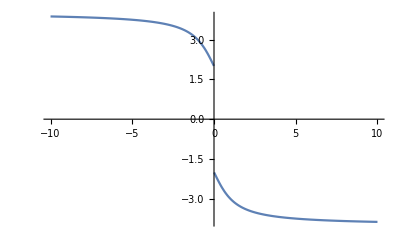

```mathematica
Plot[-(4/Pi)*Sum[ArcTan[2u+I(2-1-2k)],{k,0,2-1}],{u,-10,10}]
```

```mathematica
stringvec={3};
i=1;

Limit[Sum[If[i==j,0,Sum[Sum[Fsym[u+I(stringvec[[i]]-1-2k)/2-I(stringvec[[j]]-1-2kk)/2,-1,0],{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[i]]-1}]],{j,1,Length[stringvec]}],u->Infinity]
```

0

```mathematica
NSolve[{((ⅈ/2+Subscript[u, 1])^4(-ⅈ+Subscript[u, 1]-Subscript[u, 2]))/1-((ⅈ+Subscript[u, 1]-Subscript[u, 2])(-ⅈ/2+Subscript[u, 1])^4)/1,((ⅈ/2+Subscript[u, 2])^4(-ⅈ-Subscript[u, 1]+Subscript[u, 2]))/1-((ⅈ-Subscript[u, 1]+Subscript[u, 2])(-ⅈ/2+Subscript[u, 2])^4)/1},{Subscript[u, 1],Subscript[u, 2]}]
```

{{u_1→1.20711,u_2→1.20711},{u_1→-1.20711,u_2→-1.20711},{u_1→0.207107,u_2→0.207107},{u_1→-0.207107,u_2→-0.207107},{u_1→0.-0.500297 ⅈ,u_2→0.+0.499703 ⅈ},{u_1→0.+0.500297 ⅈ,u_2→0.-0.499703 ⅈ},{u_1→0.000282191-0.500092 ⅈ,u_2→0.000282191+0.499908 ⅈ},{u_1→0.000282191+0.500092 ⅈ,u_2→0.000282191-0.499908 ⅈ},{u_1→-0.000282191-0.500092 ⅈ,u_2→-0.000282191+0.499908 ⅈ},{u_1→-0.000282191+0.500092 ⅈ,u_2→-0.000282191-0.499908 ⅈ},{u_1→0.000174976-0.49976 ⅈ,u_2→0.000174976+0.50024 ⅈ},{u_1→0.000174976+0.49976 ⅈ,u_2→0.000174976-0.50024 ⅈ},{u_1→-0.000174976-0.49976 ⅈ,u_2→-0.000174976+0.50024 ⅈ},{u_1→-0.000174976+0.49976 ⅈ,u_2→-0.000174976-0.50024 ⅈ},{u_1→-0.288675,u_2→0.288675},{u_1→0.288675,u_2→-0.288675}}

```mathematica
Limit[{((ⅈ/2+Subscript[u, 1])^4(-ⅈ+Subscript[u, 1]-Subscript[u, 2]))/1-((ⅈ+Subscript[u, 1]-Subscript[u, 2])(-ⅈ/2+Subscript[u, 1])^4)/1,((ⅈ/2+Subscript[u, 2])^4(-ⅈ-Subscript[u, 1]+Subscript[u, 2]))/1-((ⅈ-Subscript[u, 1]+Subscript[u, 2])(-ⅈ/2+Subscript[u, 2])^4)/1},{Subscript[u, 1]->I/2,Subscript[u, 2]->-I/2}]
```

{0,0}

```mathematica
{((ⅈ/2+Subscript[u, 1])^4(-ⅈ+Subscript[u, 1]-Subscript[u, 2]))/1-((ⅈ+Subscript[u, 1]-Subscript[u, 2])(-ⅈ/2+Subscript[u, 1])^4)/1,((ⅈ/2+Subscript[u, 2])^4(-ⅈ-Subscript[u, 1]+Subscript[u, 2]))/1-((ⅈ-Subscript[u, 1]+Subscript[u, 2])(-ⅈ/2+Subscript[u, 2])^4)/1}/.{Subscript[u, 1]->0.41421356237309503+0.5 ⅈ,Subscript[u, 2]->0.41421356237309503-0.5 ⅈ}
```

General::munfl: (0.414214+1. ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (0.414214-1. ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

{0.-0.0588745 ⅈ,0.-0.0588745 ⅈ}

```mathematica
NSolve[{(ⅈ/2+Subscript[u, 1])^4/1-(-ⅈ/2+Subscript[u, 1])^4/1==0},{Subscript[u, 1]}]
```

{{u_1→-0.5},{u_1→0.},{u_1→0.5}}

```mathematica
{(ⅈ/2+Subscript[u, 1])^4/1-(-ⅈ/2+Subscript[u, 1])^4/1,(ⅈ/2+Subscript[u, 2])^4/1-(-ⅈ/2+Subscript[u, 2])^4/1}/.{Subscript[u, 1]->1,Subscript[u, 2]->1}
```

{3 ⅈ,3 ⅈ}

```mathematica
ustartNonLogGenerator[length_,magnon_,stringlength_]:=Module[{k},NSolve[Product[(u+I(stringlength-1-2k)/2+I/2)^length,{k,0,stringlength-1}]==-(-1)^stringlength Product[(u+I(stringlength-1-2kk)/2-I/2)^length,{kk,0,stringlength-1}],u]//Values];
```

```mathematica
ustartNonLogGenerator[4,2,2]
```

{{-2.41421},{-0.414214},{0.},{0.},{0.},{0.},{0.414214},{2.41421}}

```mathematica
BAENonlog[4,{2},1,1]
```

```mathematica
v[1]^4 (ⅈ+v[1])^4+v[1]^4 (-ⅈ+v[1])^4/.{v[1]->-2.414213562373095}
```

General::munfl: (-2.41421-1. ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-2.41421+1. ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

0.+0. ⅈ

```mathematica
BAENonlog[length_,stringvec_,string_,epsilon_]:=Product[(v[string]+I(stringvec[[string]]-1-2k)/2+I/2)^length,{k,0,stringvec[[string]]-1}](Product[Product[Product[(v[string]+I(stringvec[[string]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2),{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[string]]-1}],{j,1,Length[stringvec]}])^epsilon==(-1)^stringvec[[string]] Product[(v[string]+I(stringvec[[string]]-1-2k)/2-I/2)^length,{k,0,stringvec[[string]]-1}](Product[Product[Product[(v[string]+I(stringvec[[string]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2),{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[string]]-1}],{j,1,Length[stringvec]}])^epsilon;
```

```mathematica
BAENonlog[4,{2},1,1]
```

True

```mathematica
ustartNonLogGenerator[length_,stringvec_,string_]:=NSolve[BAENonlog[length,stringvec,string],v[1]]//Values
```

```mathematica
ustartNonLogGenerator[4,{2},1]
```

{{-2.41421},{-0.414214},{0.},{0.},{0.},{0.},{0.414214},{2.41421}}

```mathematica
BAElog[length_,stringvec_,string_,modenumber_,epsilon_]:=length*Sum[Fsym[2v[string]+I(stringvec[[string]]-1-2k),-1,0],{k,0,stringvec[[string]]-1}](*(-1)(-1)^stringvec[[string]]; This should not be here as log(-(-1^s)) will contribute some overall 1/2 or 0 term to the mode number, depending on the string length (1/2 if the length is even)*)-epsilon*Sum[If[string==j,0,Sum[Sum[Fsym[(v[string]+I(stringvec[[string]]-1-2k)/2-v[j]-I(stringvec[[j]]-1-2kk)/2),-1,0],{kk,0,stringvec[[j]]-1}],{k,0,stringvec[[string]]-1}]],{j,1,Length[stringvec]}]+modenumber;
```

```mathematica
BAElog[4,{2},1,3.5,1]/.v[1]->-2.414213562373095
```

0.+2.77556×10^-17 ⅈ

```mathematica
{((ⅈ/2+Subscript[u, 1])/(-ⅈ/2+Subscript[u, 1]))^4-(ⅈ+Subscript[u, 1]-Subscript[u, 2])/(-ⅈ+Subscript[u, 1]-Subscript[u, 2]),((ⅈ/2+Subscript[u, 2])/(-ⅈ/2+Subscript[u, 2]))^4-(ⅈ-Subscript[u, 1]+Subscript[u, 2])/(-ⅈ-Subscript[u, 1]+Subscript[u, 2])}/.{Subscript[u, 1]->-2.414213562373095+I/2,Subscript[u, 2]->-2.414213562373095-I/2}
```

General::munfl: (-2.41421+1. ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

General::munfl: 1/(-2.41421-1. ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

{ComplexInfinity,0.-0.728553 ⅈ}

```mathematica
{((ⅈ/2+Subscript[u, 1])^4 (ⅈ/2+Subscript[u, 2])^4)/((-ⅈ/2+Subscript[u, 1])^4 (-ⅈ/2+Subscript[u, 2])^4)-((ⅈ+Subscript[u, 1]-Subscript[u, 2]) (ⅈ-Subscript[u, 1]+Subscript[u, 2]))/((-ⅈ+Subscript[u, 1]-Subscript[u, 2]) (-ⅈ-Subscript[u, 1]+Subscript[u, 2]))}/.{Subscript[u, 1]->-2.414213562373095+I/2,Subscript[u, 2]->-2.414213562373095-I/2}
```

General::munfl: (-2.41421+1. ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/(-2.41421-1. ⅈ)^4 is too small to represent as a normalized machine number; precision may be lost.

Power::infy: Infinite expression 1/(0.+0. ⅈ) encountered.

Infinity::indet: Indeterminate expression (0.+0. ⅈ) ComplexInfinity encountered.

{Indeterminate}